## Introduction

Recently, I worked on correcting a slight misconception that pops out in a few relativity textbooks. The claim is that were a person to fall into a Schwarzschild black hole, they would survive the longest before they hit the singularity of the black hole by not doing anything, since geodesics (paths where no acceleration is applied by the observer) maximise proper time. Proper time is the time measured by the falling observer on a watch they carry. However, this explanation turns out to be misleading, since the singularity is not a single event, but a hypersurface and so the principle doesn’t apply. There is an upper bound τ = πM of proper time, but an arbitrary path will reach the singularity quicker, so using engines is advantageous.

A natural question, then, is how much time can we gain depending on the power of our spacecraft’s engines and the initial conditions of our crossing the event horizon, past which there is no escape? The details and the mathematics required to fully answer this question can be found in my recent paper, which can be found on arxiv and is currently undergoing peer review: https://arxiv.org/abs/2405.03510

In the process of this research, I have used Mathematica to create visualisations of worldlines of such a spacecraft from numerical calculations. I have also implemented methods for calculation of proper time depending on initial parameters. This notebook presents those visualisations in closer detail than the paper.

## Setup

### xAct setup

We first have to initialise xAct -- which we will use for our relativistic calculations -- and set it up to use the Schwarzschild chart. We also constrain variables to remain in the region under the event horizon.

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->16,FontColor->Black};
```

```mathematica
<<xAct`xCoba`
<<xAct`ShowTime1`;
$RecursionLimit=Infinity;
Off[General::spell];
Off[NDSolve::ndsz];
Off[InterpolatingFunction::dmval];
Off[FindRoot::cvmit];
Off[FindRoot::lstol];
Off[Reduce::ratnz];
$DefInfoQ=False;
$CVVerbose=False;
$xCobaCacheVerbose=False;
$PrePrint=ScreenDollarIndices;
$Post=ScreenDollarIndices;
$CVSimplify=Together;
$CVReplace=False;
$CovDFormat="Postfix";
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
DefManifold[M4,4,{μ,ν,α,β,σ}]
```

```mathematica
DefConstantSymbol[M]
```

```mathematica
DefChart[schw,M4, Range[0,3], {t[],r[],θ[],ϕ[]},FormatBasis->{"Partials","Differentials"},ChartColor->Red]
```

```mathematica
$Assumptions=And[
(t[]|r[]|θ[]|ϕ[])∈Reals,
2M>r[]>0,
0<=ϕ[],
M>0
];
```

```mathematica
gschw = CTensor[DiagonalMatrix[{-(1-(2M)/r[]),(1-(2M)/r[])^-1,r[]^2,(r[] Sin[θ[]])^2}],{-schw,-schw},0]
```

CTensor[{{-1+(2 M)/r,0,0,0},{0,1/(1-(2 M)/r),0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-schw,-schw},0]

```mathematica
SetCMetric[gschw,schw,SignatureOfMetric->{3,1,0}]
```

Having set up the chart, we go straight to computing the necessary geometric tensors needed for calculations (Riemann tensor, Ricci tensor, and the Christoffel symbols for the covariant derivative).

```mathematica
CDschw=CovDOfMetric[gschw]//FullSimplify;
```

```mathematica
MetricCompute[gschw,schw,All]//AbsoluteTiming
```

{0.048032,Null}

```mathematica
Christoffel[CDschw,PDschw][α,-β,-δ]//FullSimplify
```

0
M/(r (-2 M+r))
0
0 | M/(r (-2 M+r))
0
0
0 | 0
0
0
0 | 0
0
0
0
(M (-2 M+r))/r^3
0
0
0 | 0
M/(2 M r-r^2)
0
0 | 0
0
2 M-r
0 | 0
0
0
(2 M-r) Sin[θ]^2
0
0
0
0 | 0
0
1/r
0 | 0
1/r
0
0 | 0
0
0
-Cos[θ] Sin[θ]
0
0
0
0 | 0
0
0
1/r | 0
0
0
Cot[θ] | 0
1/r
Cot[θ]
0 | α |   |  
  | β | δ

```mathematica
Riemann[CDschw][-α,-β,-δ,σ]//FullSimplify
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (2 M (2 M-r))/r^4 | 0 | 0
-(2 M)/(r^2 (-2 M+r)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (M (-2 M+r))/r^4 | 0
0 | 0 | 0 | 0
M/r | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (M (-2 M+r))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(M Sin[θ]^2)/r | 0 | 0 | 0
0 | (2 M (-2 M+r))/r^4 | 0 | 0
(2 M)/(r^2 (-2 M+r)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | M/((2 M-r) r^2) | 0
0 | M/r | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | M/((2 M-r) r^2)
0 | 0 | 0 | 0
0 | (M Sin[θ]^2)/r | 0 | 0
0 | 0 | (M (2 M-r))/r^4 | 0
0 | 0 | 0 | 0
-M/r | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | M/(r^2 (-2 M+r)) | 0
0 | -M/r | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (2 M)/r
0 | 0 | -(2 M Sin[θ]^2)/r | 0
0 | 0 | 0 | (M (2 M-r))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(M Sin[θ]^2)/r | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | M/(r^2 (-2 M+r))
0 | 0 | 0 | 0
0 | -(M Sin[θ]^2)/r | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(2 M)/r
0 | 0 | (2 M Sin[θ]^2)/r | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 |   |   |   | σ
α | β | δ |

```mathematica
Ricci[CDschw][-α,-β]//FullSimplify
```

0

### Numerical calculations of geodesic equation

Now that we’re done with defining the charts, it’s time to create some worldlines. The motion is restricted to the plane.

```mathematica
$Assumptions=And[$Assumptions,θ[]==π/2]
```

(t|r|θ|ϕ)∈ℝ&&2 M>r>0&&0≤ϕ&&M>0&&θ==π/2

```mathematica
DefParameter[λ]
DefParameter[τ]
DefConstantSymbol[amag]
DefScalarFunction/@{γt,γr,γϕ,at,ar,aϕ,e,L};
```

```mathematica
x={γt[λ],γr[λ],π/2,γϕ[λ]}
u=CTensor[D[x,λ],{schw},0]
a = CTensor[ {at[λ],ar[λ],0,aϕ[λ]},{schw},0]
```

{γt[λ],γr[λ],π/2,γϕ[λ]}

CTensor[{γt'[λ],γr'[λ],0,γϕ'[λ]},{schw},0]

CTensor[{at[λ],ar[λ],0,aϕ[λ]},{schw},0]

We can also define our functions representing individual constants.

```mathematica
constants=Flatten@{Solve[u[-ν]  CTensor[{0,0,0,1},{schw},0][ν]==L[λ],γϕ'[λ]],Solve[u[-ν] CTensor[{1,0,0,0},{schw},0][ν]==e[λ]//FullSimplify,γt'[λ]]}
```

{γϕ'[λ]→L[λ]/r^2,γt'[λ]→-(e[λ] r)/(-2 M+r)}

```mathematica
u[μ]/.constants//FullSimplify
```

(e[λ] r)/(2 M-r)
γr'[λ]
0
L[λ]/r^2 | μ

In any worldline calculation, we want to use constants of motion to remove degrees of freedom. In this case, since our constants e (energy per unit mass) and L (angular momentum per unit mass) will be subject to change due to thrust applied by rocket engines, we cannot take them as constant. However, we still have the normalisation of the 4-velocity; the normalisation of the 4-acceleration; and the orthogonality of the 4-velocity to 4-acceleration.

```mathematica
unorm=First@Simplify@Solve[u[α]u[-α]==-1,γr'[λ]]
anorm=Simplify@Solve[a[α] a[-α]==amag^2,at[λ]]
aunorm=First@Simplify@Solve[a[α] u[-α]==0,ar[λ]]
```

{γr'[λ]→-(√((2 M-r) (r+(2 M-r) γt'[λ]^2+r^3 γϕ'[λ]^2)))/r}

{{at[λ]→(√(r (ar[λ]^2 r+(2 M-r) (amag^2-aϕ[λ]^2 r^2))))/(-2 M+r)},{at[λ]→(√(r (ar[λ]^2 r+(2 M-r) (amag^2-aϕ[λ]^2 r^2))))/(2 M-r)}}

{ar[λ]→((2 M-r) (at[λ] (2 M-r) γt'[λ]+aϕ[λ] r^3 γϕ'[λ]))/(r^2 γr'[λ])}

```mathematica
Solve[First[(anorm/. aunorm/. unorm/. {at[λ]->0,γt'[λ]->0}//FullSimplify)/. {Rule->Equal}],aϕ[λ]]
```

{{aϕ[λ]→-(amag √(1+r^2 γϕ'[λ]^2))/r},{aϕ[λ]→(amag √(1+r^2 γϕ'[λ]^2))/r}}

```mathematica
unorm/.constants//Simplify
```

{γr'[λ]→-(√(L[λ]^2 (-1+(2 M)/r)+r (2 M-r+e[λ]^2 r)))/r}

The important part is played by the equation of accelerated motion:

```mathematica
eqOfMotion=ParamD[λ][u[α]]+Christoffel[CDschw,PDschw][α,-β,-δ] u[β] u[δ]-a[α]
```

●
●
-Cos[θ] Sin[θ] γϕ'[λ]^2
-aϕ[λ]+(2 γr'[λ] γϕ'[λ])/r+γϕ''[λ] | α

### Auxiliary functions for display and calculation

We will need functions for prettifying the display of our graphs:

```mathematica
DisplayCartesianTPlots[plots_,labels_:{},positive_:False,M_:1]:=Module[{},
Show[
Plot[
{0},
{r,0,2M},
PlotRange->{{0,2.05M},{If[positive,-1,-25],25}},
PlotStyle->None,
GridLines->{{{1M,Directive[Gray,Thin,Dashed]},{2M,Directive[Black,Thick]}},ResourceFunction["CartesianProduct"][Range[If[positive,0,-20],20,10],{Directive[Gray,Thin,Dashed]}]},
Axes->{True,True},
AxesLabel->{MaTeX["r",Magnification->1.1], MaTeX["t",Magnification->1.1]},
AxesStyle->{Directive[Thickness[-2]],Directive[Black,Thick]},
AxesOrigin->{0,If[positive,0,-25]},
BaseStyle->texStyle,
LabelStyle->texStyle,
Ticks->{{{1M,MaTeX["1M",Magnification->1.1]},{2M,MaTeX["2M",Magnification->1.1]}},({#,MaTeX[#,Magnification->1.1]})&/@Range[If[positive,0,-20],20,10]}],
plots,
labels,
PlotRange->{{0,2.05M},{If[positive,-1,-25],25}},
PlotLabels->Automatic,
LabelStyle->texStyle,
ImageSize->Large,
TicksStyle->texStyle
]
]
Options[colorPolarAxes]={PolarAxesStyle->{},PolarLabelsStyle->{},PolarTicksStyle->{}};
colorPolarAxes[plot_Graphics,OptionsPattern[]]:=ReplaceAll[plot,{Text[Style[lbl__,{}],pos__]:>Text[Style[lbl,OptionValue[PolarLabelsStyle]],pos],Style[Line[def__],{}]:>Style[Line[def],OptionValue[PolarTicksStyle]],Circle[options__]:>Style[Circle[options],OptionValue[PolarAxesStyle]]}]
DisplayPolarPhiPlots[plots_,labels_:{},M_:1]:=Module[{},
Show[
colorPolarAxes[PolarPlot[
{2},
{r,0,2M},
PlotStyle->None,
PolarGridLines->{
ResourceFunction["CartesianProduct"][Range[0,2π,π/6],{Directive[Gray,Thick,Dashed]}],{{1M,Directive[Gray,Thick,Dashed]},{2M,Directive[Black,Thick]}}
},
PolarAxes->True,
PolarAxesOrigin->{0,2M},
PolarTicks->{({#,MaTeX[#,Magnification->1.1]})&/@Range[0,2 π-π/6,π/6],{{1M,MaTeX["1M",Magnification->1.1]},{2M,MaTeX["2M",Magnification->1.1]}}},
PlotRangeClipping->False,
PlotRangePadding->.1,
LabelStyle->texStyle,
BaseStyle->texStyle
],
PolarLabelsStyle->texStyle],
plots,
labels,
PlotRange->All,
ImageSize->Large
]
]
```

As well as a solver for our equation of motion that can return the interpolated functions representing the solution:

```mathematica
solveEquations[eqs_,u_,a_,unorm_,aeqs_,constants_,γstart_List,ustartConstants_List,amagnitude_,mass_,assumptions_]:=solveEquations[eqs,u,a,unorm,aeqs,constants,γstart,ustartConstants,amagnitude,mass,assumptions]=Block[
{$Assumptions=And[$Assumptions,assumptions,θ[]==π/2],eqTable,ustart,system,solution},
eqTable =  Table[(Simplify@eqs)[[0]][{i,schw}]==0,{i,0,3}];
ustart=Flatten@{constants/.r[]->γr[λ]/.λ->0/.ustartConstants/.γstart,Simplify[unorm/.constants/.r[]->γr[λ]]/.λ->0/.ustartConstants/.γstart};
system=Join[Select[eqTable,Not[TrueQ[#]]&]/.aeqs/.r[]->γr[λ]//Simplify,γstart,ustart]/.Rule->Equal;
solution=NDSolve[system/.{M->mass,amag->amagnitude},{γt,γr,γϕ},Join[{λ},{0,π mass}]];
Return[{solution,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[γr/.solution]}];
];
```

And, to round it off, a generator of parametric plots from a given solution:

```mathematica
CreatePlots[{solution_,λdom_},λmax_:π]:=Module[{λdomain=Min [λdom,λmax]},
Return[<|"cartesian"->ParametricPlot[{γr[λ],γt[λ]}/.solution,{λ,0,λdomain},ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->0.5,BaseStyle->texStyle,LabelStyle->texStyle],
"polar"->ParametricPlot[{γr[λ] * Cos[γϕ[λ]],γr[λ] * Sin[γϕ[λ]]}/.solution,{λ,0,λdomain},ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->1,BaseStyle->texStyle],
"cylindrical"->ParametricPlot3D[{γr[λ]*Cos[γϕ[λ]],γr[λ]*Sin[γϕ[λ]],γt[λ]}/.solution,{λ,0,λdomain},
ColorFunction->Function[{x,y,z,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],BoxRatios->{1,1,1},Boxed->False,BaseStyle->texStyle]|>
]
]
```

As we will see, overshooting with our engines is a problem. To rectify that, we need a solver that stops when optimal trajectory is reached:

```mathematica
solveEquationsUpToBestGeodesic[eqs_,u_,a_,unorm_,aeqs_,constants_,γstart_List,ustartConstants_List,amagnitude_,mass_,assumptions_,plotfunc_:γt]:=solveEquationsUpToBestGeodesic[eqs,u,a,unorm,aeqs,constants,γstart,ustartConstants,amagnitude,mass,assumptions,plotfunc]=Block[
{$Assumptions=And[$Assumptions,assumptions,θ[]==π/2],eqTable,ustart,system,solution,root,rootVals,solutionFall,solutionCombined,constantEqs,ttt,rrr,ϕϕϕ,tt,rr,ϕϕ,functions},
eqTable =  Table[(Simplify@eqs)[[0]][{i,schw}]==0,{i,0,3}];
ustart=Flatten@{constants/.r[]->γr[λ]/.λ->0/.ustartConstants/.γstart,Simplify[unorm/.constants/.r[]->γr[λ]]/.λ->0/.ustartConstants/.γstart};
system=Join[Select[eqTable,Not[TrueQ[#]]&]/.aeqs/.r[]->γr[λ]//Simplify,γstart,ustart]/.Rule->Equal;
solution=NDSolve[system/.{M->mass,amag->amagnitude},{γt,γr,γϕ},Join[{λ},{0,π mass}]];
root=Re@First@Values@FindRoot[plotfunc'[λ]/.solution,{λ,0}];
rootVals={γt[root]==N[γt[root]/.solution][[1]],γr[root]==N[γr[root]/.solution][[1]],γϕ[root]==N[γϕ[root]/.solution][[1]],plotfunc'[root]==0,γr'[root]==N[γr'[root]/.solution][[1]]};
solutionFall=NDSolve[Join[Select[eqTable,Not[TrueQ[#]]&]/.aeqs/.r[]->γr[λ]//Simplify,rootVals]/.Rule->Equal/.{M->mass,amag->0},{γt,γr,γϕ},Join[{λ,root},{π mass}]];
{ttt,rrr,ϕϕϕ}=Flatten[{γt/.solution,γr/.solution,γϕ/.solution}];
{tt,rr,ϕϕ}=Flatten[{γt/.solutionFall,γr/.solutionFall,γϕ/.solutionFall}];
functions={
γt[λ]->Piecewise[{{ttt[λ],λ<=root},{tt[λ],λ>root}}],
γr[λ]->Piecewise[{{rrr[λ],λ<=root},{rr[λ],λ>root}}],
γϕ[λ]->Piecewise[{{ϕϕϕ[λ],λ<=root},{ϕϕ[λ],λ>root}}]
};
Return[{functions,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[γr/.solutionFall]}]
];
```

## Geodesics

We will start by displaying some geodesics -- unaccelerated worldlines, or the closest thing to a straight line in curved spacetime. On all the following images that use rainbow colors, the colors depict elapsed proper time -- a.k.a. the time measured by the wristwatch of the infalling astronaut. τ = 0 is red, whereas τ = π M (which is the absolute upper bound) is blue. Each ‘tick’ corresponds to an increment of π/8 M proper time.

9.23578

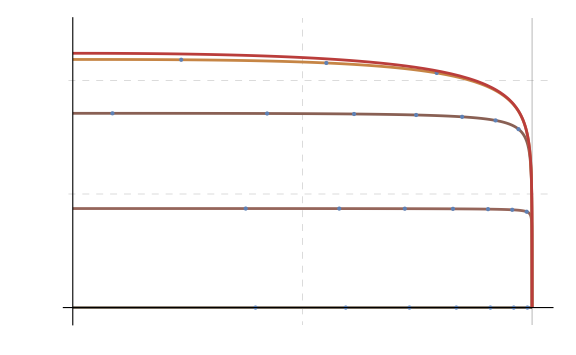

```mathematica
DisplayCartesianTPlots[Table[CreatePlots[solveEquations[eqOfMotion,u,a,unorm,{},constants[[2]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->eval,L[0]->0},0,1,And[γϕ'[λ]==γϕ''[λ]==0,aϕ[λ]==ar[λ]==at[λ]==0,L[λ]==0]]]["cartesian"],{eval,{0,0.01,0.1,1,10}}],{},True]
```

We can easily see that the ‘direct’ geodesic, corresponding to falling with no energy per unit mass e = 0 and hence having no displacement in the ∂_t  coordinate, is the one that survives the longest. Since travellers crossing from the outside of the event horizon must by definition have some non-zero e, we know engines must be useful to extend our life in practical circumstances.
Let’s see how this situation looks when we’re only taking into account angular momentum per unit mass L, with e = 0:

7.00166

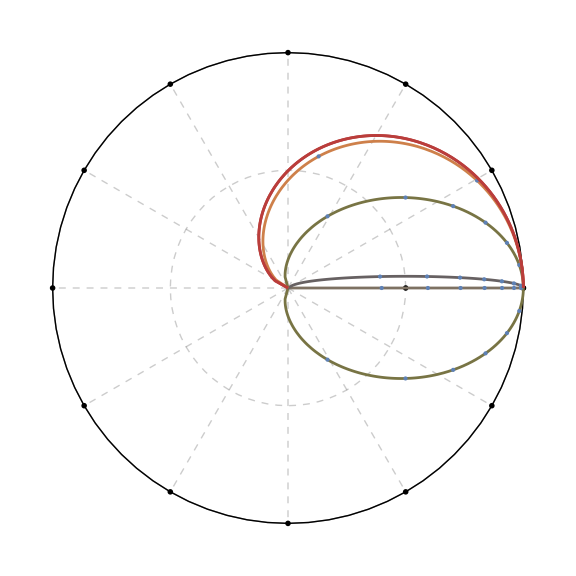

```mathematica
DisplayPolarPhiPlots[Table[CreatePlots[solveEquations[eqOfMotion,u,a,unorm,{},constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->Lval},0,1,And[γt'[λ]==γt''[λ]==0,aϕ[λ]==ar[λ]==at[λ]==0,e[λ]==0]]]["polar"],{Lval,{-1,0,0.1,1,5,100,10000}}]]
```

We can even plot multiple geodesics inside a cylinder, showing behavior in the situation with nonzero L and e.
Let’s render the orbits in real time for a c^2/^G mass black hole (roughly 2/3 the mass of Jupiter; relativists measure mass and time in meters and Jupiter happens to weigh 1.41 meters :-)), from 0 to π seconds! The upper orbits have e = 1, middle are e = 0 and lower ones are e = -0.1; for each of those, angular momentum of L = 1, L= 0 and L = -√12 is shown.

```mathematica
cylinderFrames=Table[Show[Table[CreatePlots[solveEquations[eqOfMotion, u, a, unorm,{}, constants,{γt[0]->0,γr[0]->1.99999 M,γϕ[0]->0},{e[0]->eval,L[0]->Lval},0,1,And[aϕ[λ]==ar[λ]==at[λ]==0]],λframe]["cylindrical"], {eval, {-0.1, 0, 1}}, {Lval, {-Sqrt[12], 0, 1}}],Graphics3D[{Opacity[0.2], Cylinder[{{0, 0, 25}, {0, 0, -20}}, 2], 
    Mesh -> All}], Graphics3D[{Thick, Line[{{0,0,25},{0,0,-20}}], 
    Mesh -> All}], PlotRange -> {{-2.1, 2.1}, {-2.1, 2.1}, Full}, 
  Boxed -> True,AxesLabel->{MaTeX["r",Magnification->1.1], MaTeX["r",Magnification->1.1], MaTeX["t",Magnification->1.1]}],{λframe, π/32, π, π/32}];
Dynamic[cylinderFrames[[Clock[{1,Length@cylinderFrames,1},π]]]]
```

15.4403

## Accelerated motion graphs

Let’s see how acceleration changes the outcome:

```mathematica
radialFrames=Table[
DisplayCartesianTPlots[Table[CreatePlots[solveEquations[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.r[]->γr[λ]/.aϕ[λ]->0,{at[λ],ar[λ]}][[1]]//FullSimplify,constants[[2]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->1,L[0]->0},aval,1,And[γϕ'[λ]==γϕ''[λ]==0,aϕ[λ]==0,L[λ]==0]],λframe]["cartesian"],{aval,{0,-0.65,-2.4,-10}}]],{λframe, π/32, π, π/32}];
Dynamic[radialFrames[[Clock[{1,Length@radialFrames,1},π]]]]
```

124.421

This example for radial geodesics illustrates that we can ‘overshoot’ when we apply too much acceleration, as seen in the bottom-most worldline. Same situation for angular momentum:

```mathematica
angularFrames=Table[DisplayPolarPhiPlots[Table[CreatePlots[solveEquations[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.r[]->γr[λ]/.at[λ]->0,{aϕ[λ],ar[λ]}][[1]]//FullSimplify,constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->√12},aval,1,And[γt'[λ]==γt''[λ]==0,at[λ]==0,e[λ]==0]],λframe]["polar"],{aval,{0,-0.8,-1.3}}]],{λframe, π/32, π, π/32}];
Dynamic[angularFrames[[Clock[{1,Length@angularFrames,1},π]]]]
```

62.5315

So, let’s stop accelerating the moment we kill our velocity and fall on the optimal geodesic:

```mathematica
radialOptimalFrames=Table[DisplayCartesianTPlots[Table[CreatePlots[solveEquationsUpToBestGeodesic[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.r[]->γr[λ]/.aϕ[λ]->0,{at[λ],ar[λ]}][[1]]//FullSimplify,constants[[2]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->1,L[0]->0},aval,1,And[γϕ'[λ]==γϕ''[λ]==0,aϕ[λ]==0,L[λ]==0]],λframe]["cartesian"],{aval,{0,-0.65,-2.4,-10}}],{},True],{λframe, π/8, π, π/8}];
Dynamic[radialOptimalFrames[[Clock[{1,Length@radialOptimalFrames,1},π]]]]
```

273.159

```mathematica
angularOptimalFrames=Table[DisplayPolarPhiPlots[Join[{CreatePlots[solveEquations[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.r[]->γr[λ]/.at[λ]->0,{aϕ[λ],ar[λ]}][[1]]//FullSimplify,constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->Sqrt[12]},0,1,And[γt'[λ]==γt''[λ]==0,at[λ]==0,e[λ]==0]],λframe]["polar"]},Table[CreatePlots[solveEquationsUpToBestGeodesic[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.r[]->γr[λ]/.at[λ]->0,{aϕ[λ],ar[λ]}][[1]]//FullSimplify,constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->Sqrt[12]},aval,1,And[γt'[λ]==γt''[λ]==0,at[λ]==0,e[λ]==0],γϕ],λframe]["polar"],{aval,{-0.8,-1.3}}]]],{λframe, π/8, π, π/8}];
Dynamic[angularOptimalFrames[[Clock[{1,Length@angularOptimalFrames,1},π]]]]
```

32.1109

## Direct calculation of proper time depending on circumstances

Drawing orbits is a great starting point and a good visualisation, but we’re interested in some qualitative answers.
The proper time on a geodesic is described by the following integral:

```mathematica
IntegrateWithNoAccel[mass_,est_,Lst_]:=
NIntegrate[-1/(√(est^2-(1+(Lst^2 mass^2)/y^2)(1-(2mass)/y))),{y,2mass,0}]
```

What we need is expressions for e and L depending on r; it turns out these are possible to derive and in the case of purely radial infall, we can obtain an analytic expression in terms of Carlson integrals:

```mathematica
ropt[M_,a_,e0_]:=If[a==0,-1,2M+e0/a]
CarlsonFromR[M_,a_,e0_,r_]:=Module[{z1,z2,z3,ρ},
{z1,z2,z3}=-Flatten@Values@List@ToRules@Roots[( z^3+( -(- a e0 - 2 a^2 M))z^2+(a e0 -1/(2M)+e0^2/(2M)) z^2+(-a e0/M - 2 a^2 ) z+1/(2M)a^2)==0,z]+1/r;
ρ=1/r;
2/3 CarlsonRJ[z1,z2,z3,ρ]/Sqrt[2M]]
Carlson[M_,a_,e0_]:=CarlsonFromR[M,a,e0,2M]
CarlsonOptimal[M_,a_,e0_]:=Module[{rbang},
If[a==0,
Carlson[M,0,e0],
rbang=ropt[M,a,e0];
If[2M>=rbang>0,
Carlson[M,a,e0]-CarlsonFromR[M,a,e0,rbang]+CarlsonFromR[M,0,0,rbang],
Carlson[M,a,e0]
]
]
]
```

In the case of infall with e = 0, we do not have an analytic expression but can nevertheless obtain a simple numerical integral:

```mathematica
rLopt[M_,a_,L0_]:=If[a==0,z==-1,Reduce[L0-a(-1/2 √(-1+(2 M)/z) z (3 M+z)-3 M^2 ArcTan[√(-1+(2 M)/z)])==0,{z},Reals]]
NτLR[M_,a_,L0_,r_]:=NIntegrate[-(1/(√(-(1+1/z^2(L0-a(-1/2 √(-1+(2 M)/z) z (3 M+z)-3 M^2 ArcTan[√(-1+(2 M)/z)]))^2)(1-(2M)/z)))),{z,r,0}]
NτL[M_,a_,L0_]:=NτLR[M,a,L0,2M]
NτLOptimal[M_,a_,L0_]:=Module[{rbang},
rbang=rLopt[M,a,L0];
If[Not[BooleanQ[rbang]] && 2M>=rbang[[2]]>=0,
NτL[M,a,L0]-NτLR[M,a,L0,rbang[[2]]]+NτLR[M,0,0,rbang[[2]]],
NτL[M,a,L0]
]
]
```

In the general case, we have to use an explicit quadrature and adjust at every step as the equations have a single degree of freedom corresponding to the way we control our spacecraft and thus don’t admit explicit solutions. The optimal way to thrust turns out to be always opposite to the 3-velocity in the frame of an optimally falling observer with e = L = 0.

```mathematica
de[r_,a_]:=Module[{},-a]
dL[r_,a_,M_]:=Module[{},-(r a)/(√((2M)/r-1))]
Quadrature[e0_,L0_,M_,a_,cuts_:10000]:=Module[{
sum=0,
dr=(1.9999M)/cuts,
rcur ,
Lcur =L0*M,
ecur=e0,
angle,
at,aphi,
γ },
γ= √(L^2/r^2+1+e^2((2M)/r-1)^-1);
rcur=1.99995M;
While[rcur>0.00005,
sum=sum+N[dr/(γ √((2M)/r-1))/.{L->Lcur,e->ecur,r->rcur}];
angle=If[Lcur==0,π/2,ArcTan[(rcur ecur)/(Lcur √((2M)/rcur-1))]];
at = - Sin[angle]*a;
aphi = - Cos[angle]*a;
ecur=If[ecur>0,ecur+de[rcur,at]*dr,0];
Lcur=If[Lcur>0,Lcur+dL[rcur,aphi,M]*dr,0];
rcur=rcur-dr;
];
sum]
```

## Potential gains

Equipped with the ways to calculate proper time directly, we could ask ourselves: how much can we really gain? For this purpose, we will use some realistic values for acceleration (on the order of g to 1000g; see paper for longer discussion), and the black hole masses for Sagittarius A*, Messier 87*, and Phoenix A* (the largest black hole found in nature). We use geometric units:

```mathematica
g=10/((3*10^8)^2)
```

1/9000000000000000

```mathematica
sol=1500
```

1500

For radial infall, for parameters e = 1 (free fall from far away from the black hole) and e = 10 (colliding with the black hole at high relativistic speeds):

```mathematica
ColumnForm[Flatten[Table[{M[[2]],a[[2]],"e = "<>ToString[e],
Quantity[CarlsonOptimal[M[[1]],a[[1]],e]/(3*10^8)//N//Re,"Seconds"],Quantity[CarlsonOptimal[M[[1]],a[[1]],e]/(3*10^8*60*60)//N//Re,"Hours"],Quantity[100*((CarlsonOptimal[M[[1]],a[[1]],e]//N//Re)/(CarlsonOptimal[M[[1]],0,e]//N//Re)-1),"Percent"]},{M,{{4.297*10^6*sol,"Sagittarius A*"},{6.5*10^9*sol,"Messier 87"},{10^11 sol, "Phoenix A"}}},{a,{{0,"0g"},{-g,"1g"},{-10g,"10g"},{-100g,"100g"},{-1000g,"1000g"}}},{e,{1,10}}],2]]
```

{Sagittarius A*,0g,e = 1,28.6467 s,0.00795741 h,0. %}
{Sagittarius A*,0g,e = 10,4.20983 s,0.0011694 h,0. %}
{Sagittarius A*,1g,e = 1,28.6467 s,0.00795741 h,0.0000245543 %}
{Sagittarius A*,1g,e = 10,4.20184 s,0.00116718 h,-0.189891 %}
{Sagittarius A*,10g,e = 1,28.6467 s,0.00795743 h,0.000245543 %}
{Sagittarius A*,10g,e = 10,4.20978 s,0.00116938 h,-0.00113972 %}
{Sagittarius A*,100g,e = 1,28.6474 s,0.0079576 h,0.00245546 %}
{Sagittarius A*,100g,e = 10,4.20986 s,0.0011694 h,0.000576047 %}
{Sagittarius A*,1000g,e = 1,28.6537 s,0.00795936 h,0.0245571 %}
{Sagittarius A*,1000g,e = 10,4.21011 s,0.00116948 h,0.00666028 %}
{Messier 87,0g,e = 1,43333.3 s,12.037 h,0. %}
{Messier 87,0g,e = 10,6368.14 s,1.76893 h,-1.11022×10^-14 %}
{Messier 87,1g,e = 1,43349.4 s,12.0415 h,0.0371494 %}
{Messier 87,1g,e = 10,6368.78 s,1.76911 h,0.0100768 %}
{Messier 87,10g,e = 1,43494.6 s,12.0818 h,0.372073 %}
{Messier 87,10g,e = 10,6374.57 s,1.77071 h,0.100875 %}
{Messier 87,100g,e = 1,44968.4 s,12.4912 h,3.77328 %}
{Messier 87,100g,e = 10,6433.12 s,1.78698 h,1.02042 %}
{Messier 87,1000g,e = 1,58099.7 s,16.1388 h,34.0762 %}
{Messier 87,1000g,e = 10,7103.64 s,1.97323 h,11.5496 %}
{Phoenix A,0g,e = 1,666667. s,185.185 h,0. %}
{Phoenix A,0g,e = 10,97971.4 s,27.2143 h,0. %}
{Phoenix A,1g,e = 1,670486. s,186.246 h,0.572948 %}
{Phoenix A,1g,e = 10,98123.6 s,27.2565 h,0.155299 %}
{Phoenix A,10g,e = 1,705633. s,196.009 h,5.84496 %}
{Phoenix A,10g,e = 10,99520.2 s,27.6445 h,1.58082 %}
{Phoenix A,100g,e = 1,965345. s,268.151 h,44.8018 %}
{Phoenix A,100g,e = 10,116886. s,32.4684 h,19.3065 %}
{Phoenix A,1000g,e = 1,1.30164×10^6 s,361.567 h,95.2463 %}
{Phoenix A,1000g,e = 10,636771. s,176.881 h,549.956 %}

We see that we can get some significant gains, especially in the case of slamming into the black hole at relativistic speeds. Let’s also pick parameters corresponding to a ‘realistic’ infall resulting from, say, some accident in an orbit nearby a black hole: e = 0.8 and L = √12M  are the interesting factors here:

```mathematica
ColumnForm[Flatten[Table[{M[[2]],a[[2]],Quantity[Quadrature[0.8,Sqrt[12],M[[1]],a[[1]],10000]/(3*10^8)//N//Re,"Seconds"],Quantity[Quadrature[0.8,Sqrt[12],M[[1]],a[[1]],10000]/(3*10^8*60*60)//N//Re,"Hours"],Quantity[100*((Quadrature[0.8,Sqrt[12],M[[1]],a[[1]],10000]//N//Re)/(Quadrature[0.8,Sqrt[12],M[[1]],0,10000]//N//Re)-1),"Percent"]},{M,{{4.297*10^6*sol,"Sagittarius A*"},{6.5*10^9*sol,"Messier 87"},{10^11 sol, "Phoenix A"}}},{a,{{0,"0g"},{-g,"1g"},{-10g,"10g"},{-100g,"100g"},{-1000g,"1000g"}}}],1]]
```

44.8055

{Sagittarius A*,0g,16.1555 s,0.00448763 h,0. %}
{Sagittarius A*,1g,16.1555 s,0.00448763 h,0.0000256068 %}
{Sagittarius A*,10g,16.1555 s,0.00448764 h,0.000256068 %}
{Sagittarius A*,100g,16.1559 s,0.00448774 h,0.00256076 %}
{Sagittarius A*,1000g,16.1596 s,0.00448878 h,0.0256153 %}
{Messier 87,0g,24438.1 s,6.78836 h,0. %}
{Messier 87,1g,24447.6 s,6.79099 h,0.0387544 %}
{Messier 87,10g,24533.2 s,6.81479 h,0.389309 %}
{Messier 87,100g,25435.1 s,7.06532 h,4.07985 %}
{Messier 87,1000g,45134. s,12.5372 h,84.6872 %}
{Phoenix A,0g,375971. s,104.436 h,0. %}
{Phoenix A,1g,378229. s,105.064 h,0.600574 %}
{Phoenix A,10g,400272. s,111.187 h,6.46374 %}
{Phoenix A,100g,951137. s,264.205 h,152.982 %}
{Phoenix A,1000g,1.33118×10^6 s,369.771 h,254.064 %}

In the most extreme case, we more than triple our survival time!

### Radial infall gains

Using these, we can draw some graphs of proper time depending on parameters:

```mathematica
dataCarlsonOptimal=Flatten[Table[{a,e0,CarlsonOptimal[1,a,e0]//N//Re},{a,-5,0,0.05},{e0,0,5,0.05}],1];
dataCarlsonGain=({#[[1]],#[[2]],#[[3]]/IntegrateWithNoAccel[1,#[[2]],0]})&/@dataCarlsonOptimal;
```

7.40995

43.861

2.85482

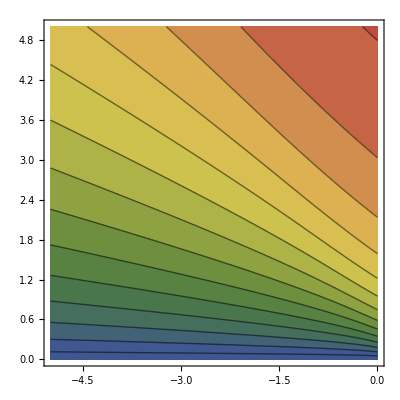

```mathematica
ListContourPlot[dataCarlsonOptimal,ColorFunction->(ColorData["DarkRainbow"][1-#/π]&),ColorFunctionScaling->False,Contours->Range[π,0,-π/16],PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\tau [m]"],LabelStyle->texStyle,FrameLabel->MaTeX/@{"\\alpha [m^{-1}]","e_0"},PlotRange->All,FrameStyle->Black]
```

We also want to see the graphs for the gain function:

1.3644

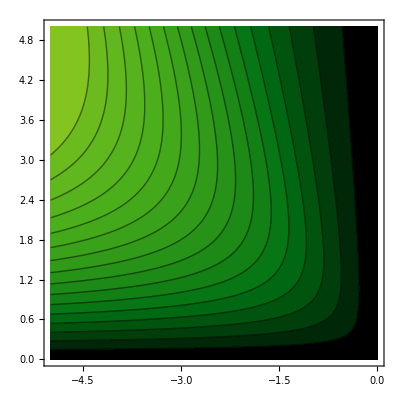

```mathematica
ListContourPlot[dataCarlsonGain,Contours->16,ColorFunction->(ColorData["AvocadoColors"][Log[5,#]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\frac{\\tau}{\\tau_{\\alpha=0}}"],BaseStyle->texStyle,LabelStyle->texStyle,FrameLabel->MaTeX/@{"\\alpha [m^{-1}]","e_0"},PlotRange->All,FrameStyle->Black]
```

### Infall with e = 0 gains

Similarly, we can do this for the situation of angular momentum only:

```mathematica
dataNLOptimal=Flatten[Table[{a,L0,NτLOptimal[1,a,L0]//N//Re},{a,-5,0,0.5/10},{L0,0,5,0.5/10}],1];
dataNLGain=({#[[1]],#[[2]],#[[3]]/IntegrateWithNoAccel[1,0,#[[2]]]})&/@dataNLOptimal;
```

1545.35

26.5765

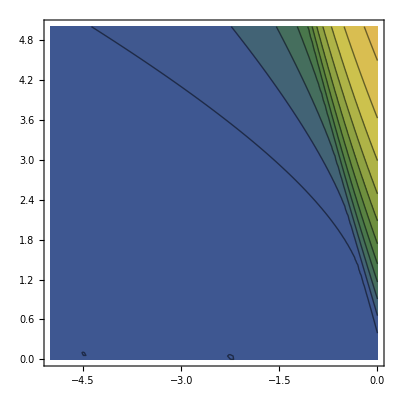

```mathematica
ListContourPlot[dataNLOptimal,ColorFunction->(ColorData["DarkRainbow"][1-#/π]&),ColorFunctionScaling->False,Contours->Range[π,0,-π/16],PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\tau [m]"],LabelStyle->texStyle,BaseStyle->texStyle,FrameLabel->MaTeX/@{"\\alpha [m^{-1}]","L_0 [M]"},PlotRange->All,FrameStyle->Black]
```

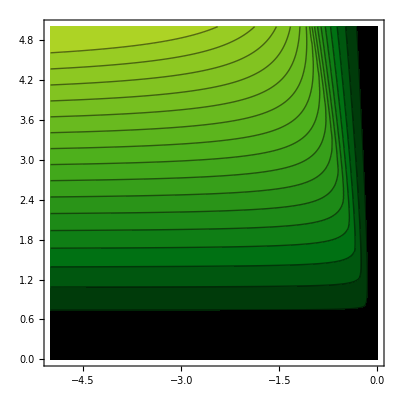

```mathematica
ListContourPlot[dataNLGain,Contours->16,ColorFunction->(ColorData["AvocadoColors"][Log[5,#]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\frac{\\tau}{\\tau_{\\alpha=0}}"],BaseStyle->texStyle,LabelStyle->texStyle,FrameLabel->MaTeX/@{"\\alpha [m^{-1}]","L_0 [M]"},PlotRange->All,FrameStyle->Black]
```

### General case gains

And to round it all off, we have the general case. Let’s plot the proper time and gain for the acceleration of a = -1 m^-1 in geometric units.

```mathematica
genPlotsGeneralCase[a_,M_:1,ticks_:100,quads_:10000]:=Module[{
generalPlotData,
generalGain
},
generalPlotData=Flatten[Table[{L0,e0,Quadrature[e0,L0,M,a,quads]},{L0,0,5,5/ticks},{e0,0,5,5/ticks}],1];
generalGain=({#[[1]],#[[2]],#[[3]]/IntegrateWithNoAccel[M,#[[2]],#[[1]]]})&/@generalPlotData;
Return[
{ListContourPlot[generalPlotData,ColorFunction->(ColorData["DarkRainbow"][1-#/(π M)]&),ColorFunctionScaling->False,Contours->Range[π M,0,-π M/16],PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\tau [m]"],BaseStyle->texStyle,LabelStyle->texStyle,FrameLabel->MaTeX/@{"L_0 [M]","e_0"},PlotRange->All,FrameStyle->Black],
ListContourPlot[generalGain,Contours->16,ColorFunction->(ColorData["AvocadoColors"][Log[5,#]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\frac{\\tau}{\\tau_{\\alpha=0}}"],BaseStyle->texStyle,LabelStyle->texStyle,FrameLabel->MaTeX/@{"L_0 [M]","e_0"},PlotRange->All,FrameStyle->Black]
}
]
]
```

4072.82

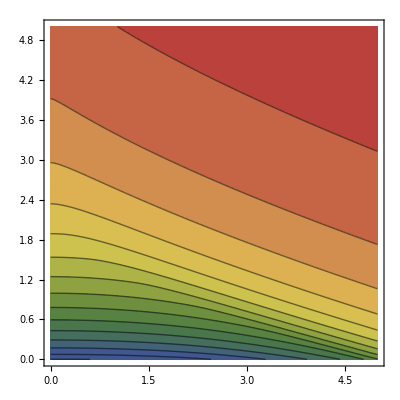
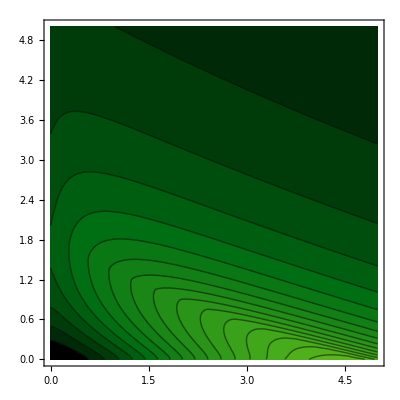

```mathematica
genPlotsGeneralCase[-1]
```

## Conclusion

The presented visualisations, while a very nice way to understand a little about this problem of extending survival time under the event horizon of a black hole, are only one part. I strongly recommend checking out the paper for a more indepth look: https://arxiv.org/abs/2405.03510